# Linearity

```mathematica
theoreticalColor="TropicalRainForest";
experimentalColor="Bittersweet";
lineFitColor = "Green";
histogramColor="Asparagus";
zeroFreqColor="Razzmatazz";
zeroFreqColorAtF = "ShamRock";
```

## Observation

```mathematica
experimentalList={{0.5,23/1000},{1,47/1000},{1.67, 78/1000},{2,95/1000 },{3,169/1000},{4,193/1000},{5,233/1000},{6,288/1000},{7,315/1000},{8,391/1000},{9,441/1000},{10,469/1000},{11, 559/1000},{12, 602/1000},{13, 637/1000},{14,714/1000},{15,774/1000},{16, 839/1000},{16.7, 893/1000},{17,912/1000},{18,957/1000},{19,989/1000},{20,997/1000}};
```

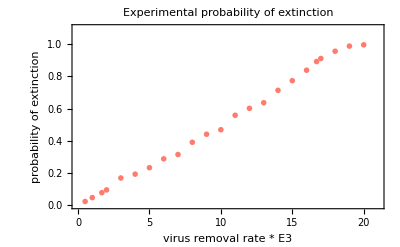

```mathematica
ListPlot[
experimentalList,
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.010]},
Background->Lighter[Gray, 1.0],
Frame->True,
PlotLabel->Style["Experimental probability of extinction",FontSize->14],
PlotMarkers->{{●,10}},PlotRange->{{0,21},{0,1.1}},
FrameLabel->{{"probability of extinction",""},{"virus removal rate * E3",""}},
PlotLabel->"Experimental probability of extinction"]
```

```mathematica
lineFit=Fit[experimentalList,{1,x},x]
```

-0.0186912+0.0526277 x

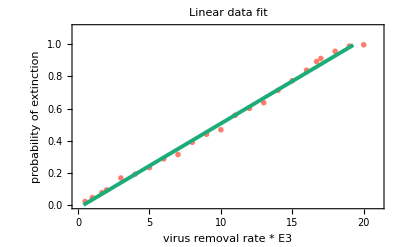

```mathematica
Show[
ListPlot[experimentalList,
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.10]},
Frame->True,
PlotLabel->"Linear data fit",
FrameLabel->{{"probability of extinction",""},{"virus removal rate * E3",""}},
PlotMarkers->{{●,10}},PlotRange->{{0,21},{0,1.1}}],Plot[lineFit,{x,0.38705,19.2705}, PlotStyle->{ColorData["Crayola"][lineFitColor ],Thickness[0.007]}]]
```

```mathematica
Solve[lineFit==1,x]
```

{{x→19.3566}}

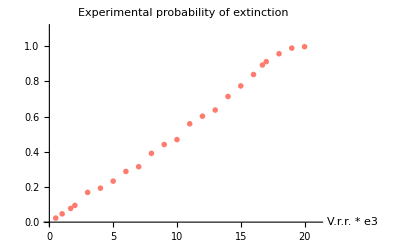

```mathematica
PlotExperimental=ListPlot[experimentalList, 
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},PlotRange->{{0,21},{0,1.1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"Experimental probability of extinction"]
```

note: for the majority of the curve above we see ~reasonable linearity, the end seems mollified. Towards the end (vrr = 19, 20) we don’t really have E(X)>>1, so the fix point theorem does not hold in itself. (and it is the fix point theorem that gives us linearity at this point)

## Offspring distribution

#### Virus removal rate \in [1.67 , 18] * E-3

```mathematica
VRRString = "20";
VRRNumString="20";
```

```mathematica
data =Import["C:\\Users\\juhaszn\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo"<>VRRString<>".txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0}}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,493},{1,276},{2,113},{3,62},{4,35},{5,12},{6,5},{7,3},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,1}}

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

0.956

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->ColorData["Crayola"]["GrannySmithApple"],PlotLabel->"VRR="<>VRRNumString<>"E-3. Shown against geometric distr., Freq. Zero"];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},
PlotStyle->ColorData["Crayola"]["PineGreen"],
PlotMarkers->Automatic];
```

```mathematica
probabilityData[[1,2]]/1000 //N
```

0.493

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

Gábor ötlete: geom param: mintaátlag reciproka, ML becslés; K-S próba.
Végeredmény: melyik param becslés ad jobb illeszkedést.

```mathematica
geoParamMLE=1/(Mean[cleanData]+1)
```

0.511247

```mathematica
Max[cleanData]
```

17.

```mathematica
geoParamMLE
```

0.511247

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->ColorData["Crayola"]["GrannySmithApple"],PlotLabel->"VRR="<>VRRNumString<>"E-3. Shown against geometric distr., MLE"];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geoParamMLE],x]//Evaluate,{x,0,Max[cleanData]},
PlotStyle->ColorData["Crayola"]["PineGreen"],
PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

#### Virus removal rate = very small, i.e. 0.5*E-3: in this case it loses the nice geometrical fit

```mathematica
data =Import["C:\\Users\\juhaszn\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo0dot5.txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=2,i<=2*dataLength, i=i+2,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData;
```

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData;
```

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

40.463

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartLegends->{"Offspring histogram, VRR=3*E-3."},ChartStyle->"Pastel",PlotLabel->"Shown against geometric distr."];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

```mathematica
geoParamMLE=1/(Mean[cleanData]+1)
```

0.0241179

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geoParamMLE],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

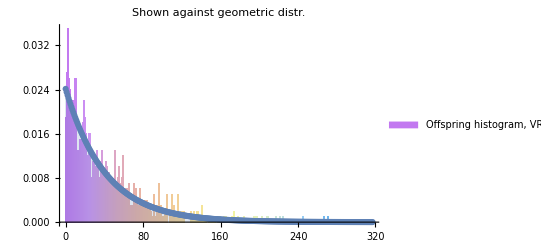

```mathematica
Show[p1,p2]
```

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

## The Maximum Likelihood estimate of the parameter of the geometric distribution.

```mathematica
vrrrangemax=19.27049965956595;
```

```mathematica
MLEstList={{1.67,0.07431},{2.0,0.091424},{3,0.128617},{4,0.167476},{5,0.1970055},{6,0.219202104340201},{7,0.26752273},{8,0.27708506},{9,0.318167},{10,0.3246753},{11,0.338180},{12,0.386548},{13,0.392772},{15,0.443852},{16.7, 0.468603},{18,0.47664},{20,0.5112474}};
```

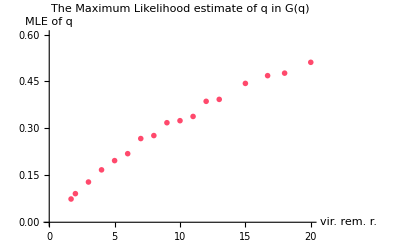

```mathematica
PlotMLEList=ListPlot[MLEstList, 
PlotStyle->{ColorData["Crayola"]["RadicalRed"],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{0,0.6},
PlotRange->{{0,vrrrangemax},{0,1}},AxesLabel->{"vir. rem. r.","MLE of q"},PlotLabel->"The Maximum Likelihood estimate of q in G(q)"]
```

This looks similar to part of the 1/(1+(a/x)^n) curve -- Hill equation with n=1:

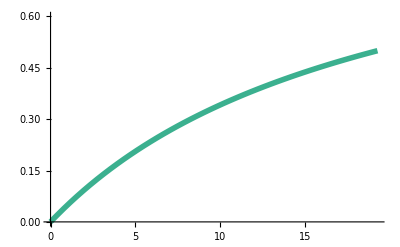

```mathematica
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,0,vrrrangemax},PlotStyle->{ColorData["Crayola"]["JungleGreen"],Thickness[0.010]},PlotRange->{0,0.6}]
```

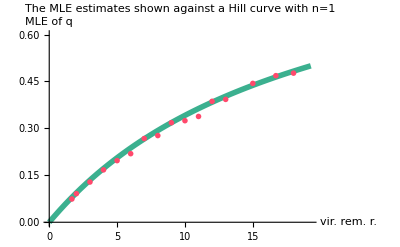

```mathematica
PlotMLEList=ListPlot[MLEstList, 
PlotStyle->{ColorData["Crayola"]["RadicalRed"],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{0,0.6},
AxesLabel->{"vir. rem. r.","MLE of q"},PlotLabel->"The MLE estimates shown against a Hill curve with n=1"];
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,0,vrrrangemax},
PlotLabel->"The MLE estimates shown against a Hill curve with n=1",
AxesLabel->{"vir. rem. r.","MLE of q"},
PlotStyle->{ColorData["Crayola"]["JungleGreen"],Thickness[0.010]},PlotRange->{0,0.6}];
Show[ curvePlot,PlotMLEList]
```

Observation nr2: at this point we have a concave function.

## Branching processes: the theoretical PoE

Using the above observation regarding a reasonable fit to geometrical distribution, the PoE is given by the fix point of the PGF of the geometrical distribution.

The POE is given by

G_X(q)=q
q / (1 - (1-q)x) = x, thus we have
q = x * (1 - (1-q)x) 

We have a simple second order equation. The non-negative solution to that is:

```mathematica
Rasterize[Plot[N[(1-Sqrt[1-4*(1-(q))*(q)])/(2*(1-(q)))],{q,0,1},
PlotStyle->{ColorData["Crayola"]["JungleGreen"],Thickness[0.010]},PlotLabel->"The G_X(q)(x)=x fixpoint eq.'s solution for geo. distr. with param. q",AxesLabel->{"q","PoE"}]]
```

-Graphics-

We have seen that q = q(mu), where we found that q = q(mu) takes the following form: q(mu) = 1 / (1 + 19.27/mu)

Altogether we have

q / (1 - (1-q)x) = x and
q(mu) = 1 / (1 + 19.27/mu)

The probability of extinction is given (below on the LHS) as a function of q (the relative frequency of 0 offsprings), and for that to be a linear function of mu we need the following:

```mathematica
Solve[(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))==(1/c)*mu,q]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{q→mu/(c+mu)}}

Which corresponds to what we have previously observed.

## Theoretical linearity

```mathematica
PoE[q_]:=(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))
```

```mathematica
qMLE[mu_]:=1/(1 + (19.33)/mu)
```

```mathematica
POEqMLE={{0.5,PoE[qMLE[0.5]]},{1.0,PoE[qMLE[1.0]]},{2.0,PoE[qMLE[2.0]]},{3,PoE[qMLE[3.0]]},{4,PoE[qMLE[4.0]]},{5,PoE[qMLE[5]]},{6,PoE[qMLE[6]]},{7,PoE[qMLE[7]]},{8,PoE[qMLE[8]]},{9,PoE[qMLE[9]]},{10,PoE[qMLE[10]]},{11,PoE[qMLE[11]]},{12,PoE[qMLE[12]]},{13,PoE[qMLE[13]]},{14,PoE[qMLE[14]]},{15,PoE[qMLE[15]]},{16,PoE[qMLE[16]]},{16.7, PoE[qMLE[16.7]]},{17,PoE[qMLE[17]]},{18,PoE[qMLE[18]]},{19,PoE[qMLE[19]]},{20,PoE[qMLE[20]]}};
```

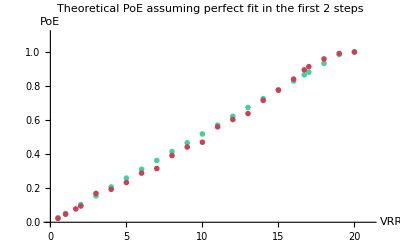

```mathematica
PlotZeroFreqAtF=ListPlot[{POEqMLE,experimentalList}, 
PlotStyle->{{ColorData["Crayola"]["ShamRock"],Thickness[0.010]},{ColorData["Crayola"]["BrickRed"],Thickness[0.010]}},
PlotMarkers->{{●,10}},
PlotRange->{{0,21},{0,1.1}},AxesLabel->{"VRR","PoE"},PlotLabel->"Theoretical PoE assuming perfect fit in the first 2 steps"]
```